# Heavy neutrino decays

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (development version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/matheushostert/Repos/stdHNL/calculations

```mathematica
dm[mu_]:=GA[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
PR=dm[6];
PL=dm[7];
dσ[μ_,ν_]:=I/2(dm[μ].dm[ν]-dm[ν].dm[μ]);
SetOptions[{DiracMatrix, DiracSlash,LeviCivita, FourVector, MetricTensor, SetMandelstam, OneLoop, ScalarProduct},Dimension->4];
```

## Amplitudes

## ν_h (k1) -->l_β-(k2) l_α+(k3) v_i (k4)

```mathematica
MajAmp=-eQED* dij *2* SpinorUBar[k4,m4] .(dσ[μ,γ].fv[k1-k4,γ]).PL.((1+h dm[5]. ds[s])/2).SpinorU[k1,m1] * SpinorUBar[k2,m2].dm[ν].SpinorV[k3,m3]*mt[μ,ν]/(Pair[Momentum[k3+k2],Momentum[k2+k3]]);
```

```mathematica
MajAmpC =-eQED* dij *2*-I/2 ComplexConjugate[SpinorUBar[k4,m4] .(dm[μ].dm[γ]-dm[γ].dm[μ]).fv[k1-k4,γ].PL.((1+h dm[5]. ds[s])/2).SpinorU[k1,m1]]*mt[μ,ν]/(Pair[Momentum[k3+k2],Momentum[k3+k2]])ComplexConjugate[SpinorUBar[k2,m2].dm[ν].SpinorV[k3,m3]]/.{μ-> μ2,ν-> ν2};
```

## Spin sums and Trace

```mathematica
MajAmpSQR = FermionSpinSum[MajAmpC MajAmp]//Simplify;
```

```mathematica
TracedMajAmpSQR = ((MajAmpSQR/.{DiracTrace-> Tr}/.{k4-> k1 -k2-k3}//Contract)//Simplify)/.h^2-> 1;
TracedMajAmpSQRsummed =( (TracedMajAmpSQR/.h-> 1)+(TracedMajAmpSQR/. h-> -1)//FullSimplify)/.h^2-> 1;
```

# Kinematics

## Substitute kinematical variables

```mathematica
Lambda[a_,b_, c_] := (a-b-c)^2-4b c
subP = {Pair[Momentum[k1],Momentum[k1]]-> m1^2,
Pair[Momentum[k2],Momentum[k2]]->m2^2,
Pair[Momentum[k3],Momentum[k3]]->m3^2,
Pair[Momentum[k4],Momentum[k4]]->m4^2,
Pair[Momentum[k1],Momentum[k2]]->(-m34sqr+m1^2+m2^2)/2,
Pair[Momentum[k1],Momentum[k3]]->-1/2(m24sqr - m1^2-m3^2),
Pair[Momentum[k1],Momentum[k4]]->(-m23sqr+m1^2+m4^2)/2,
Pair[Momentum[k2],Momentum[k3]]->(m23sqr-m2^2-m3^2)/2,
Pair[Momentum[k2],Momentum[k4]]->(m24sqr-m4^2-m2^2)/2,
Pair[Momentum[k3],Momentum[k4]]->(m34sqr-m4^2-m3^2)/2,
Pair[Momentum[s],Momentum[s]]-> -1,
Pair[Momentum[k1],Momentum[s]]-> 0,
Pair[Momentum[k2],Momentum[s]]-> k3CM*c3+k4CM*c4,
Pair[Momentum[k3],Momentum[s]]-> -k3CM *c3,
Pair[Momentum[k4],Momentum[s]]-> -k4CM*c4};

subPexpressions={
k4CM->m1/2 √Lambda[1,m23sqr/m1^2,m4^2/m1^2],k3CM->m1/2 √Lambda[1,m24sqr/m1^2,m3^2/m1^2],
k2CM->m1/2 √Lambda[1,m34sqr/m1^2,m2^2/m1^2]};

subEexpressions={
E4CM->(m1^2+m4^2-m23sqr)/(2m1),E3CM->(m1^2+m3^2-m24sqr)/(2m1),
E2CM->(m1^2+m2^2-m34sqr)/(2m1)};

subC4expressions={c4-> c3*c34-√(1-c3*c3)*√(1-c34*c34)*cphi34};

subC34expressions={c34-> (m23sqr+m24sqr-m2*m2-m1*m1+2*E3CM*E4CM)/(2*k3CM*k4CM)};

subMassNorm ={m1-> 1  m1,m2-> x2 m1, m3-> x3 m1, m4 -> x4 m1, m24sqr-> x24 m1^2,m23sqr-> x23 m1^2, m34sqr-> x34 m1^2,MW-> xWBOSON m1,MZBOSON-> xZBOSON m1, MZPRIME-> xZPRIME m1};
```

## phase space

```mathematica
PS3 = 1/(32 m1^2 (2 π)^5);
FluxFactor=1/(2 m1);
SpinAverage = 1/2;
```

### Substitute in the special cases

```mathematica
subMasslessNorm={x2-> 0, x3->0,x4-> 0};
subMassless={m1-> mh,m2-> 0, m3->0,m4-> 0};
subGf={gweak-> √((8 Gf MW^2)/(√2))};
subAlphaQED={eQED-> √(alphaQED*4π)};
subINTEGRATION={m34sqr-> m1^2+m2^2+m3^2+m4^2-m24sqr-m23sqr };
subgLgR=(Solve[Ca== gL-gR&&Cv==gL+gR,{gL,gR}])[[1]];
subCvCa={Ca-> -1/2,Cv-> (-1/2+2 Sin[W]^2)};
subCW=(Solve[Gf/(√2)-gweak^2/(8 cw^2 MZBOSON^2)==0,{cw}]//Simplify//PowerExpand)[[1]];
submasses={m1-> mh,m4-> 0,m3-> mlep, m2-> mlep};
```

## Full Expression

```mathematica
FULL = TracedMajAmpSQR* PS3*FluxFactor*4 π^2*2/.subP/.subPexpressions/.subINTEGRATION//ExpandAll//Cancel//Simplify;
FULLAVE = TracedMajAmpSQRsummed* PS3*FluxFactor*4 π^2*2/.subP/.subPexpressions/.subINTEGRATION//ExpandAll//Cancel//Simplify;
```

```mathematica
Needs["ToPython`"]
```

```mathematica
Export["N_to_nu_ee_dipole.dat",ToPython[FULLAVE/.{m1-> mh,m4-> mf,m2-> mm, m4-> mp,m24sqr-> u,m23sqr-> t},"np"]]
```

N_to_nu_ee_dipole.dat

### Limiting cases

## SM CC only

```mathematica
dGammaHelMassless= FULLAVE/.subMassless/.subAlphaQED//Simplify//PowerExpand
dGammaHel= FULLAVE/.submasses/.subAlphaQED//Simplify//PowerExpand
```

(alphaQED dij^2 (2 m23sqr m24sqr-m23sqr mh^2+2 m24sqr^2-2 m24sqr mh^2+mh^4))/(4 π^2 m23sqr mh^3)

(alphaQED dij^2 (m23sqr^2 (2 m24sqr-mh^2-2 mlep^2)+m23sqr (2 m24sqr^2-2 m24sqr (mh^2+2 mlep^2)+mh^4+2 mlep^4)+2 mh^4 mlep^2))/(4 π^2 m23sqr^2 mh^3)

```mathematica
(((dGammaHelMassless/(2π*2)/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{m24sqr-> u,m23sqr-> t}//PowerExpand//Simplify//PowerExpand//Simplify
(((dGammaHel/(2π*2)/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{m24sqr-> u,m23sqr-> t}//PowerExpand//Simplify//PowerExpand//Simplify
```

(alphaQED dij^2 (-mh^2 (t+2 u)+mh^4+2 u (t+u)))/(16 π^3 mh^3 t)

(alphaQED dij^2 (mh^4 (2 mlep^2+t)-mh^2 t (t+2 u)-2 t (mlep^2-u) (-mlep^2+t+u)))/(16 π^3 mh^3 t^2)

### Dgamma / dE+ dE-

```mathematica
Integrate[Integrate[(((dGammaHelMassless/(2π*2)*4 mh^2/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{m24sqr-> u,m23sqr-> t}/.{cphi34-> Cos[phi34]}//FullSimplify,{phi34,0,2π}],{c3,-1,1}]/.{u-> mh^2-2 mh Eminus,t->- mh^2 + 2mh (Eplus+Eminus) }/.subEexpressions//FullSimplify
```

(2 alphaQED dij^2 (mh (Eminus+Eplus)-4 Eminus Eplus))/(π^2 (2 (Eminus+Eplus)-mh))

### Total rate

```mathematica
Ep =(t+m1^2-m4^2)/(2 √t);E2 =-(t-m3^2+m2^2)/(2 √t);
PP = √(Ep^2-m1^2);P2 = √(E2^2-m2^2);
umin = m1^2+m2^2-2*Ep*E2+2*PP*P2/.submasses//Simplify//PowerExpand//Simplify
umax = m1^2+m2^2-2*Ep*E2-2*PP*P2/.submasses//Simplify//PowerExpand//Simplify
```

1/2 (((t-mh^2) √(t-4 mlep^2))/(√t)+3 mh^2+2 mlep^2+t)

1/2 (((mh^2-t) √(t-4 mlep^2))/(√t)+3 mh^2+2 mlep^2+t)

```mathematica
dGammadudtMassless = Integrate[Integrate[(((dGammaHelMassless/(2π*2)/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{m24sqr-> u,m23sqr-> t}/.{cphi34-> Cos[phi34]}//FullSimplify,{phi34,0,2π}],{c3,-1,1}]//FullSimplify
dGammadudt = Integrate[Integrate[(((dGammaHel/(2π*2)/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{m24sqr-> u,m23sqr-> t}/.{cphi34-> Cos[phi34]}//FullSimplify,{phi34,0,2π}],{c3,-1,1}]//FullSimplify
```

(alphaQED dij^2 (-mh^2 (t+2 u)+mh^4+2 u (t+u)))/(4 π^2 mh^3 t)

(alphaQED dij^2 (mh^4 (2 mlep^2+t)-mh^2 t (t+2 u)-2 t (mlep^2-u) (-mlep^2+t+u)))/(4 π^2 mh^3 t^2)

```mathematica
dGammadtMassless=Integrate[dGammadudtMassless,{u,myumin,myumax},Assumptions->{myumax>myumin&&myumin>0&&m1> 0&&t<myumax&&t>myumin&&t<m1^2}]/.myumin-> umin/.myumax-> umax/.{mlep-> 0}//Simplify//ExpandAll//FullSimplify
dGammadt=Integrate[dGammadudt,{u,myumin,myumax},Assumptions->{myumax>myumin&&myumin>0&&m1> 0&&t<myumax&&t>myumin&&t<m1^2}]/.myumin-> umin/.myumax-> umax//Simplify//ExpandAll//FullSimplify
```

(alphaQED dij^2 (mh^2-t) (11 mh^2 t+8 mh^4+5 t^2))/(12 π^2 mh^3 t)

(alphaQED dij^2 √(t-4 mlep^2) (4 mh^6 (mlep^2+2 t)+3 mh^4 t (t-2 mlep^2)-6 mh^2 t^3+t^3 (2 mlep^2-5 t)))/(12 π^2 mh^3 t^(5/2))

```mathematica
finalgammaMassless=Integrate[dGammadtMassless,{t,4 mlep^2,mh^2},Assumptions->{mh> 0&&t∈Reals&&t<mh^2&&mlep>0&&mh> 2mlep}]
finalgamma=Integrate[dGammadt,{t,4 mlep^2,mh^2},Assumptions->{mh> 0&&t∈Reals&&t<mh^2&&mlep>0&&mh> 2mlep}]
```

-(alphaQED dij^2 (36 mh^4 mlep^2-144 mh^2 mlep^4+24 mh^6 log((4 mlep^2)/mh^2)+5 mh^6-320 mlep^6))/(36 π^2 mh^3)

(alphaQED dij^2 (mh √(mh^2-4 mlep^2) (18 mh^2 mlep^2-17 mh^4+8 mlep^4)-8 (-3 mh^4 mlep^2+3 mh^2 mlep^4+2 mh^6+4 mlep^6) log((2 mlep)/(√(mh^2-4 mlep^2)+mh))))/(12 π^2 mh^3)

```mathematica
finalgammacutMassless=Integrate[dGammadtMassless,{t,minMee^2,mh^2},Assumptions->{mh> 0&&t∈Reals&&t<mh^2&&mlep>0&&mh> 2mlep&&minMeeSQR>0&&minMee<mh&&minMee>2mlep&&minMee∈Reals}]
```

(alphaQED dij^2 (-9 mh^4 minMee^2+9 mh^2 minMee^4+48 mh^6 log(mh/minMee)-5 mh^6+5 minMee^6))/(36 π^2 mh^3)

```mathematica
finalgammacut=Integrate[dGammadt,{t,minMee^2,mh^2},Assumptions->{mh> 0&&t∈Reals&&t<mh^2&&mlep>0&&mh> 2mlep&&minMeeSQR>0&&minMee<mh&&minMee>2mlep&&minMee∈Reals}]
```

1/(12 π^2 mh^3)alphaQED dij^2 (-(5120 ⅈ mlep^9 -9/2-3/2-1/2mh^2/(4 mlep^2))/(3 mh^3)-(9728 ⅈ mlep^9 -5/2-3/2-1/2mh^2/(4 mlep^2))/mh^3+(18944 ⅈ mlep^9 -3/2-3/2-1/2mh^2/(4 mlep^2))/(3 mh^3)+(512 ⅈ mlep^7 (mh^2+13 mlep^2) -7/2-3/2-1/2mh^2/(4 mlep^2))/mh^3-(1536 ⅈ mlep^7 -5/2-3/2-1/2mh^2/(4 mlep^2))/mh+(1536 ⅈ mlep^7 -3/2-3/2-1/2mh^2/(4 mlep^2))/mh+64 ⅈ mh mlep^5 -5/2-3/2-1/2mh^2/(4 mlep^2)-96 ⅈ mh mlep^5 -3/2-3/2-1/2mh^2/(4 mlep^2)-128/3 ⅈ mh^3 mlep^3 -3/2-3/2-1/2mh^2/(4 mlep^2)-6 mh^2 minMee mlep^2 √(minMee^2-4 mlep^2)-(12 mh^4 mlep^2 √(minMee^2-4 mlep^2))/minMee+(8 mh^6 mlep^2 √(minMee^2-4 mlep^2))/(3 minMee^3)+3 mh^2 minMee^3 √(minMee^2-4 mlep^2)-3 mh^4 minMee √(minMee^2-4 mlep^2)+(46 mh^6 √(minMee^2-4 mlep^2))/(3 minMee)-24 ⅈ mh^2 mlep^4 csc^-1((2 mlep)/minMee)+24 ⅈ mh^4 mlep^2 csc^-1((2 mlep)/minMee)-16 ⅈ mh^6 csc^-1((2 mlep)/minMee)+(768 mlep^8 √(mh^2-4 mlep^2))/mh^3+(64 mlep^6 √(mh^2-4 mlep^2))/mh-80 mh mlep^4 √(mh^2-4 mlep^2)-20 mh^3 mlep^2 √(mh^2-4 mlep^2)+6 mh^5 √(mh^2-4 mlep^2)-8 minMee mlep^4 √(minMee^2-4 mlep^2)-8/3 minMee^3 mlep^2 √(minMee^2-4 mlep^2)+5/3 minMee^5 √(minMee^2-4 mlep^2)-32 ⅈ mlep^6 csc^-1((2 mlep)/minMee))

```mathematica
normalizedfinalgamma =finalgamma/.{mlep-> (r*mh)/2}//Simplify//PowerExpand//Simplify
```

```mathematica
-(alphaQED dij^2 mh^2 ((r^6+3 r^4-12 r^2+32) (-log(mh+ⅈ mh √(r^2-1))+log(mh)+log(r))- √(1 - r^2) (r^4+9 r^2-34)))/(24 π^2)
```

```mathematica
normalizedfinalgamma =finalgamma/.{mlep-> r*mh}//Simplify//PowerExpand//Simplify
normalizedfinalgammacutMassless =finalgammacutMassless/.{mlep-> r*mh}/.{minMee-> mh*reemin}//Simplify//PowerExpand//Simplify
normalizedfinalgammacut =Simplify[finalgammacut/.{mlep-> r*mh}/.{minMee-> mh*reemin}//Simplify,Assumptions->{reemin>0&&r>0}]//PowerExpand//FullSimplify
```

-(alphaQED dij^2 mh^2 (mh √(1-4 r^2) (-8 r^4-18 r^2+17)+8 mh (4 r^6+3 r^4-3 r^2+2) (-log(mh (√(1-4 r^2)+1))+log(mh)+log(r)+log(2))))/(12 π^2)

(alphaQED dij^2 mh^3 (5 reemin^6+9 reemin^4-9 reemin^2-48 log(reemin)-5))/(36 π^2)

1/(36 π^2 reemin^3)alphaQED dij^2 mh^3 (2304 ⅈ √(4-1/r^2) r^9 reemin^3+2304 √(1-4 r^2) r^8 reemin^3+192 ⅈ √(4-1/r^2) r^7 reemin^3+192 √(1-4 r^2) r^6 reemin^3-264 ⅈ √(4-1/r^2) r^5 reemin^3-24 r^4 reemin^3 (reemin √(reemin^2-4 r^2)+10 √(1-4 r^2))-114 ⅈ √(4-1/r^2) r^3 reemin^3-2 r^2 (reemin^2 (reemin (reemin (4 reemin^2+9) √(reemin^2-4 r^2)+30 √(1-4 r^2))+18 √(reemin^2-4 r^2))-4 √(reemin^2-4 r^2))+69 ⅈ √(4-1/r^2) r reemin^3+reemin^2 (reemin (reemin (5 reemin^4+9 reemin^2-9) √(reemin^2-4 r^2)+18 √(1-4 r^2))+46 √(reemin^2-4 r^2))+24 ⅈ (4 r^6+3 r^4-3 r^2+2) reemin^3 (csc^-1(2 r)-csc^-1((2 r)/reemin)))

```mathematica
normalizedfinalgammacutNOIMAG=Simplify[Simplify[normalizedfinalgammacut, Assumptions->{reemin>=2*r&&r>0&&reemin>0&&r<1/2&&reemin<1}]//Simplify//PowerExpand]/.Arg-> Identity//FullSimplify
```

1/(36 π^2 reemin^3)alphaQED dij^2 mh^3 (5 reemin^8 √(reemin^2-4 r^2)+(9-8 r^2) reemin^6 √(reemin^2-4 r^2)-3 (8 r^4+6 r^2+3) reemin^4 √(reemin^2-4 r^2)+3 √(1-4 r^2) (8 r^4+18 r^2-17) reemin^3+2 (23-18 r^2) reemin^2 √(reemin^2-4 r^2)+8 r^2 √(reemin^2-4 r^2)+24 ⅈ (4 r^6+3 r^4-3 r^2+2) reemin^3 (csc^-1(2 r)-csc^-1((2 r)/reemin)))

```mathematica
approx3body=Series[normalizedfinalgamma,{r,0,1}]//Normal//FullSimplify
approx3bodycutMassless=Series[normalizedfinalgammacutMassless,{r,0,2}]//Normal
approx3bodycut=Series[normalizedfinalgammacut,{r,0,8},Assumptions->{reemin>0&&r>0}]//Normal//Simplify//PowerExpand//FullSimplify
```

-(alphaQED dij^2 mh^3 (16 log(r)+17))/(12 π^2)

(alphaQED dij^2 mh^3 (5 reemin^6+9 reemin^4-9 reemin^2-48 log(reemin)-5))/(36 π^2)

-1/(36 π^2 reemin^8)alphaQED dij^2 mh^3 (24 (4 r^6+3 r^4-3 r^2+2) reemin^8 log(reemin)-(reemin^2-1) (6 r^8 (-23 reemin^6-2 reemin^4+13 reemin^2+12)+8 r^6 reemin^2 (-4 reemin^4+5 reemin^2+5)+18 r^4 reemin^4 (-reemin^4+reemin^2+2)-18 r^2 reemin^6 (reemin^4+3 reemin^2-2)+reemin^8 (5 reemin^4+14 reemin^2+5)))

```mathematica
CoefficientList[approx3body,r^2]/.{alphaQED-> 1/137,r->(511*10^-6)/ 0.1}//Simplify//PowerExpand//Simplify
```

{-(alphaQED dij^2 mh^3 (16 log(r)+17))/(12 π^2)}

```mathematica
normalizedfinalgamma//Cancel//FullSimplify
```

(alphaQED dij^2 mh^3 (-8 (4 r^6+3 r^4-3 r^2+2) (-log(mh (√(1-4 r^2)+1))+log(2 mh)+log(r))+8 √(1-4 r^2) r^4+18 √(1-4 r^2) r^2-17 √(1-4 r^2)))/(12 π^2)

```mathematica
-8 (4 r^6+3 r^4-3 r^2+2) Log[(2r)/(√(1-4 r^2)+1) ]+8 √(1-4 r^2) r^4+18 √(1-4 r^2) r^2-17 √(1-4 r^2)//FullSimplify
```

√(1-4 r^2) (8 r^4+18 r^2-17)-8 (4 r^6+3 r^4-3 r^2+2) log((2 r)/(√(1-4 r^2)+1))

```mathematica
8 (4 r^6+3 r^4-3 r^2+2) Log[(√(1-4 r^2)+1)/(2r)]+8 √(1-4 r^2) r^4+18 √(1-4 r^2) r^2-17 √(1-4 r^2)/.r-> 0.4//N
```

0.596272

```mathematica
-8 (4 r^6+3 r^4-3 r^2+2) Log[(2r)/(√(1-4 r^2)+1)]/.r-> 0.4
```

8.94539

```mathematica
16*(Log[1/r]-1)-1/.r-> 0.3//N
16*(Log[1/r]-1)-1/.r-> 0.3//N
```

2.26356

```mathematica
Solve[16*Log[r]+17== 0&&r>0&&r<1/2,r]
```

{{r→1/ⅇ^(17/16)}}

```mathematica
1/ⅇ^(17/16)//N
```

0.345591

```mathematica
Log[(511*10^-6)/ 0.1]//FullSimplify
```

-5.27656

```mathematica
GZ=mh^5*U2/(192 π^3)Gf^2;twobodydecay =(mh^3 dij^2)/(4π);
```

```mathematica
approx3bodycut/twobodydecay/.reemin-> 2 r/.{alphaQED-> 1/137,r->(511*10^-6)/ 0.1}//Simplify//PowerExpand//Simplify
```

0.10636

```mathematica
ratiocutapprox[reemin_]:=Evaluate[approx3bodycut/twobodydecay/.{alphaQED-> 1/137,r->(511*10^-6)/ 0.1}//Simplify//PowerExpand//Simplify]
ratiocut[reemin_]:=Evaluate[normalizedfinalgammacutNOIMAG/twobodydecay/.{alphaQED-> 1/137,r->(511*10^-6)/ 0.1}//Simplify//PowerExpand//Simplify]
```

```mathematica
ratiocut[(511*10^-6)/ 0.1*10]
ratiocutapprox[(511*10^-6)/ 0.1*10]
```

0.0795247

0.0709234

```mathematica
approx3body/twobodydecay/.{alphaQED-> 1/137,r->(511*10^-6)/ 0.1}//N
```

0.104434

```mathematica
Gratio[r_] :=Evaluate[ normalizedfinalgamma/twobodydecay/.alphaQED-> 1/137//PowerExpand//Simplify//Cancel//FullSimplify]
```

```mathematica
Expansion[r_] :=Evaluate[ approx3body/twobodydecay/.alphaQED-> 1/137//PowerExpand//Simplify//Cancel//FullSimplify]
```

100

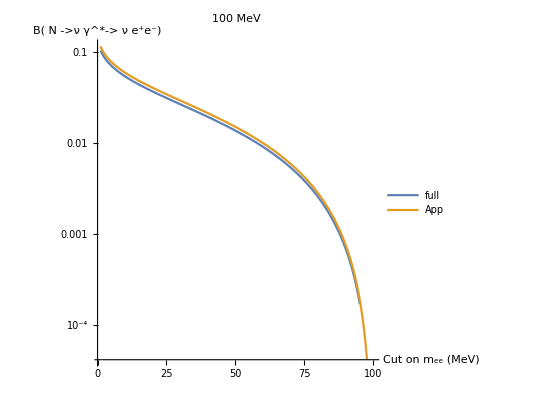

```mathematica
mN = 100
LogPlot[{ratiocut[x/mN],1.1*ratiocutapprox[x/mN]},{x,2*(511*10^-3),mN}, AxesLabel->{"Cut on m_ee (MeV)","B( N ->ν γ^*-> ν e^+e^-)"},AspectRatio->1,PlotLabel->mN" MeV",PlotLegends->{"full","App"}]
```

```mathematica
/
```

```mathematica
"
```

```mathematica
LogPlot[{Gratio[x],Expansion[x],ratiocut[2*x]},{x,(511*10^-6)/ 0.1,0.48}, PlotLegends->{"Cut"}]
```

### Printing

```mathematica
ToPython[approx3bodycut,"np"]
```

-1/36 * alphaQED * ( dij )**( 2 ) * ( mh )**( 3 ) * ( np.pi )**( -2 ) * ( reemin )**( -8 ) * ( -1 * ( -1 + ( reemin )**( 2 ) ) * ( 8 * ( r )**( 6 ) * ( reemin )**( 2 ) * ( 5 + ( 5 * ( reemin )**( 2 ) + -4 * ( reemin )**( 4 ) ) ) + ( 18 * ( r )**( 4 ) * ( reemin )**( 4 ) * ( 2 + ( ( reemin )**( 2 ) + -1 * ( reemin )**( 4 ) ) ) + ( -18 * ( r )**( 2 ) * ( reemin )**( 6 ) * ( -2 + ( 3 * ( reemin )**( 2 ) + ( reemin )**( 4 ) ) ) + ( ( reemin )**( 8 ) * ( 5 + ( 14 * ( reemin )**( 2 ) + 5 * ( reemin )**( 4 ) ) ) + 6 * ( r )**( 8 ) * ( 12 + ( 13 * ( reemin )**( 2 ) + ( -2 * ( reemin )**( 4 ) + -23 * ( reemin )**( 6 ) ) ) ) ) ) ) ) + 24 * ( 2 + ( -3 * ( r )**( 2 ) + ( 3 * ( r )**( 4 ) + 4 * ( r )**( 6 ) ) ) ) * ( reemin )**( 8 ) * np.log( reemin ) )

```mathematica
Export["full_nuee_dipole.txt",ToPython[normalizedfinalgammacutNOIMAG,"np"]]
```

full_nuee_dipole.txt

```mathematica
normalizedfinalgammacutNOIMAG
```

1/(36 π^2 reemin^3)alphaQED dij^2 mh^3 (5 reemin^8 √(reemin^2-4 r^2)+(9-8 r^2) reemin^6 √(reemin^2-4 r^2)-3 (8 r^4+6 r^2+3) reemin^4 √(reemin^2-4 r^2)+3 √(1-4 r^2) (8 r^4+18 r^2-17) reemin^3+2 (23-18 r^2) reemin^2 √(reemin^2-4 r^2)+8 r^2 √(reemin^2-4 r^2)+24 ⅈ (4 r^6+3 r^4-3 r^2+2) reemin^3 (csc^-1(2 r)-csc^-1((2 r)/reemin)))

```mathematica
ToPython[normalizedfinalgammacutNOIMAG,"np"]
```

1/36 * alphaQED * ( dij )**( 2 ) * ( mh )**( 3 ) * ( np.pi )**( -2 ) * ( reemin )**( -3 ) * ( 3 * ( ( 1 + -4 * ( r )**( 2 ) ) )**( 1/2 ) * ( -17 + ( 18 * ( r )**( 2 ) + 8 * ( r )**( 4 ) ) ) * ( reemin )**( 3 ) + ( 8 * ( r )**( 2 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( 2 * ( 23 + -18 * ( r )**( 2 ) ) * ( reemin )**( 2 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( -3 * ( 3 + ( 6 * ( r )**( 2 ) + 8 * ( r )**( 4 ) ) ) * ( reemin )**( 4 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( ( 9 + -8 * ( r )**( 2 ) ) * ( reemin )**( 6 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( 5 * ( reemin )**( 8 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + complex( 0,24 ) * ( 2 + ( -3 * ( r )**( 2 ) + ( 3 * ( r )**( 4 ) + 4 * ( r )**( 6 ) ) ) ) * ( reemin )**( 3 ) * ( np.arccsc( 2 * r ) + -1 * np.arccsc( 2 * r * ( reemin )**( -1 ) ) ) ) ) ) ) ) )